```mathematica
SetDirectory[NotebookDirectory[]];
path1=FindFile["gravity_phi_leg1.txt"];
path2=FindFile["mass_phi_leg1.txt"];
path3=FindFile["gravity_phi_leg2.txt"];
path4=FindFile["mass_phi_leg2.txt"];
path5=FindFile["gravity_phi_leg3.txt"];
path6=FindFile["mass_phi_leg3.txt"];
path7=FindFile["gravity_heave_leg1.txt"];
path8=FindFile["mass_heave_leg1.txt"];
path9=FindFile["gravity_heave_leg2.txt"];
path10=FindFile["mass_heave_leg2.txt"];
path11=FindFile["gravity_heave_leg3.txt"];
path12=FindFile["mass_heave_leg3.txt"];
```

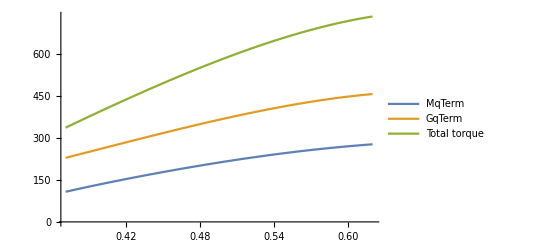

```mathematica
(* Importing data *)
data1=Import[path7, "Table"];
data2=Import[path8, "Table"];
data3=Transpose[{data1[[;;,1]],data1[[;;,2]]+data2[[;;,2]]}];
ListLinePlot[{data1,data2,data3},PlotRange->Automatic,PlotLegends->{"MqTerm","GqTerm","Total torque"}]
```

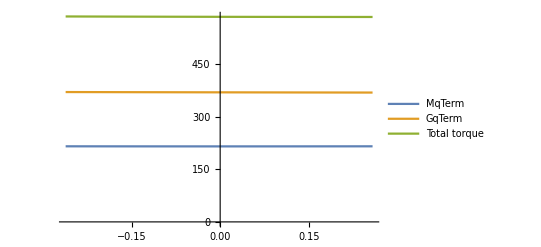

```mathematica
(* Importing data *)
data1=Import[path1, "Table"];
data2=Import[path2, "Table"];
data3=Transpose[{data1[[;;,1]],data1[[;;,2]]+data2[[;;,2]]}];
ListLinePlot[{data1,data2,data3},PlotRange->Automatic,PlotLegends->{"MqTerm","GqTerm","Total torque"}]
```